# Solving ODEs and DAEs with NDSolve

The Wolfram Language™ has extensive capabilities for solving differential equations both symbolically and numerically. This section covers:

Introduction to solving differential equations

Solving differential equations numerically with NDSolve

Specifying boundary conditions

Features and options of NDSolve

## Introduction to Solving Differential Equations

### Symbolic Solutions

With DSolve, the symbolic solution for many types of differential equations can be found.

Nonlinear Differential Equations:

```mathematica
DSolve[y''[x]==3y[x] y'[x] + (3 y[x]^2 + 4 y[x]+1),y[x],x][[1]]//Column//FullSimplify
```

y[x]→((ⅈ √6 √(ⅇ^(-2 x)) √C[1]-6 C[2]) Cosh[√(3/2) √(ⅇ^(-2 x)) √C[1]]+(-3 ⅈ+2 √6 √(ⅇ^(-2 x)) √C[1] C[2]) Sinh[√(3/2) √(ⅇ^(-2 x)) √C[1]])/(6 C[2] Cosh[√(3/2) √(ⅇ^(-2 x)) √C[1]]+3 ⅈ Sinh[√(3/2) √(ⅇ^(-2 x)) √C[1]])

Partial Differential Equations (PDEs):

```mathematica
BurgersEqn=D[u[x,t],t]+u[x,t]D[u[x,t],x]==ν D[u[x,t],{x,2}];
```

```mathematica
sol=DSolve[{BurgersEqn,u[x,0]==UnitBox[x]},u[x,t],{x,t}][[1]]//FullSimplify
```

{u[x,t]→(ⅇ^((1+t)/(4 ν)) (-Erf[(-1+2 t-2 x)/(4 √(t ν))]+Erf[(1+2 t-2 x)/(4 √(t ν))]))/(ⅇ^((1+t)/(4 ν)) (Erfc[(-1+2 t-2 x)/(4 √(t ν))]-Erfc[(1+2 t-2 x)/(4 √(t ν))])+ⅇ^(x/(2 ν)) (Erfc[(1-2 x)/(4 √(t ν))]+ⅇ^(1/2/ν) Erfc[(1+2 x)/(4 √(t ν))]))}

```mathematica
Plot3D[Evaluate[u[x,t]/.sol/.ν->1],{x,0,2},{t,0,1},ColorFunction->"Rainbow",PlotPoints->50,PlotRange->All]
```

-Graphics3D-

System of Equations:

```mathematica
A={{4,6},{1,-1}};
```

```mathematica
X[t_]={x[t],y[t]};
```

```mathematica
DSolve[X'[t]==A.X[t],X[t],t]//Column
```

{x[t]→1/7 ⅇ^(-2 t) (1+6 ⅇ^(7 t)) C[1]+6/7 ⅇ^(-2 t) (-1+ⅇ^(7 t)) C[2],y[t]→1/7 ⅇ^(-2 t) (-1+ⅇ^(7 t)) C[1]+1/7 ⅇ^(-2 t) (6+ⅇ^(7 t)) C[2]}

Differential Algebraic Equations (DAEs):

```mathematica
DSolve[{x'[t]==x[t]+2y[t],y[t]==x[t]+2^t,x[t]+z[t]==0},{x[t],y[t],z[t]},t][[1]]
```

{x[t]→1/8 (-ⅇ^(3 t) C[1]+(16 ⅇ^(3 t+t (-3+Log[2])))/(-3+Log[2])),y[t]→2^t+1/8 (-ⅇ^(3 t) C[1]+(16 ⅇ^(3 t+t (-3+Log[2])))/(-3+Log[2])),z[t]→1/8 (ⅇ^(3 t) C[1]-(16 ⅇ^(3 t+t (-3+Log[2])))/(-3+Log[2]))}

### Asymptotic Solutions

Beginning in Version 11.3, asymptotic methods have been implemented. This provides a third method for solving differential equations (aside from exact symbolic solutions with DSolve and numeric solutions with NDSolve).

With AsymptoticDSolveValue, the asymptotic solution at infinity of the nonlinear equation presented in the previous subsection can be found:

```mathematica
AsymptoticDSolveValue[y''[x]==3y[x] y'[x] + (3 y[x]^2 + 4 y[x]+1),y[x],{x,Infinity,2}]//FullSimplify
```

-1+(√(2/3) ⅇ^-x √C[1] (-2 C[2]+Cot[√(3/2) ⅇ^-x √C[1]]))/(1+2 C[2] Cot[√(3/2) ⅇ^-x √C[1]])

Similar to AsymptoticDSolveValue, AsymptoticIntegrate provides asymptotic solutions for integrals.

Similar functions like AsymptoticSolve, AsymptoticRSolveValue and AsymptoticSum provide a third method to solve a particular problem, complementing the analogous symbolic and numeric functions.

### Numeric Solutions

Not all differential equations have symbolic solutions. In such a case, numeric solutions should be sought with NDSolve.

Finding numeric solutions to differential equations with NDSolve will be the focus of the rest of this course.

The types of differential equations that can be solved depend on the region over which a solution is sought.

#### Rectangular Regions

Rectangular regions are:

• Lines in 1D 
• Rectangle boxes in 2D 
• Cuboid boxes in 3D
• n-dimensional boxes in n dimensions

NDSolve can solve both linear and nonlinear PDEs up to any order when solving over rectangular regions using the method of lines and tensor product grid.

#### Arbitrarily Shaped Regions

When solving over arbitrarily shaped regions, NDSolve will use the finite element method (FEM). The types of equations that can be solved with FEM fall into a general form:

m∂^2/(∂t^2)u+d∂/(∂t)u+∇·(-c ∇u-α⃗ u+γ⃗) +β⃗·∇u+ a u -f=0.

```mathematica
Clear["Global`*"]
```

## Basics of Using NDSolve

When using NDSolve, the initial or boundary conditions must be sufficient to determine a unique solution. For ODEs of a single dependent variable, the number of conditions must equal the highest-order derivative:

```mathematica
eqn=y'[x]+y[x]+Sin[x]==0;
cond=y[0]==0;
```

```mathematica
sol=NDSolveValue[{eqn,cond},y[x],{x,-Pi,3Pi}]
```

InterpolatingFunction[…][x]

With arguments:

equation and function conditions

function to solve for

range of the independent variable.

Solutions are given in terms of InterpolatingFunction. They can be visualized using Plot and other similar functions:

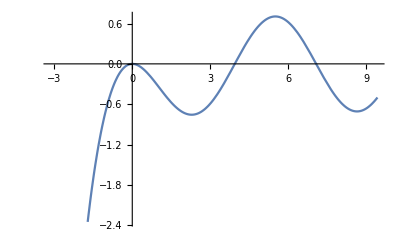

```mathematica
Plot[sol,{x,-Pi,3Pi}]
```

Further processing and operations can be performed on the InterpolatingFunction. For example, derivatives and integrals can be computed:

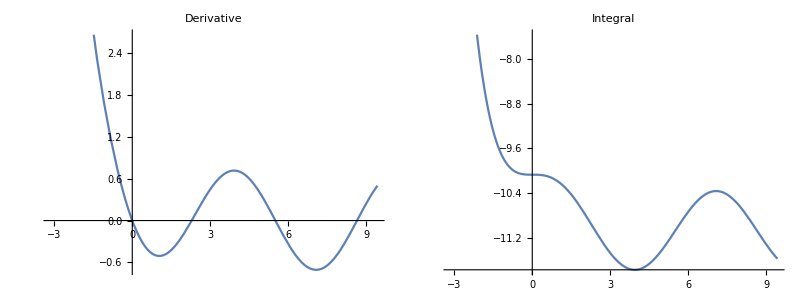

```mathematica
Grid[{{
Plot[Evaluate[D[sol,x]],{x,-Pi,3Pi},PlotLabel->"Derivative"],
Plot[Evaluate[∫solⅆx],{x,-Pi,3Pi},PlotLabel->"Integral"]
}}]
```

NDSolve is very reliable. Nonetheless, it is important to verify results. With the preceding example, you can put the solution into the left-hand side of the equation and plot the result to show that it approximately equals zero everywhere:

```mathematica
verify=eqn[[1]]/.{y[x]->sol,y'[x]->D[sol,x]};
```

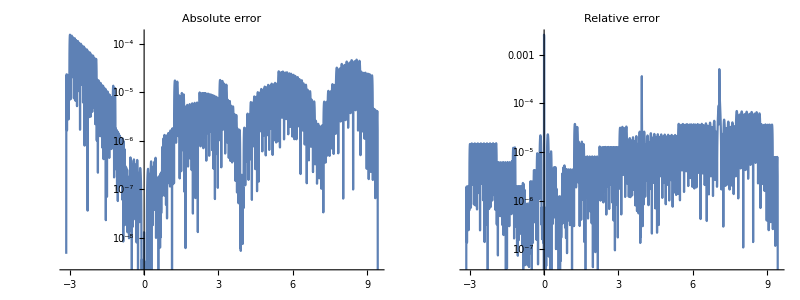

```mathematica
Grid[{{
LogPlot[Abs[verify],{x,-Pi,3Pi},PlotLabel->"Absolute error"],
LogPlot[Abs[verify/sol],{x,-Pi,3Pi},PlotLabel->"Relative error"]
}}]
```

It is also possible to specify vectorial variables in NDSolve:

```mathematica
sol1=NDSolve[{n[0]=={.1,1},r[0]==1,r'[t]==0,n'[t]=={2 r[t],4 r[t]}},{n[t],r[t]},{t,0,100}]
```

{{n[t]→InterpolatingFunction[…][t],r[t]→InterpolatingFunction[…][t]}}

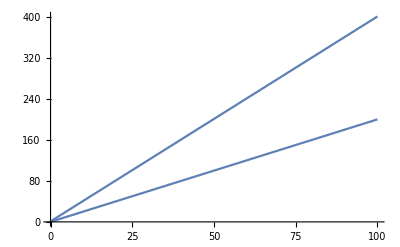

```mathematica
Plot[n[t]/.sol1,{t,0,100},PlotStyle->Small]
```

```mathematica
Clear["Global`*"]
```

## NDSolve versus NDSolveValue

NDsolve and NDSolveValue both do the exact same calculation. The only difference between the two functions is how the output is presented:

```mathematica
eqn=y'[x]+y[x]+Sin[x]==0;
cond=y[0]==0;
solNDSolve=NDSolve[{eqn,cond},y[x],{x,-π,3π}];
solNDSolveValue=NDSolveValue[{eqn,cond},y[x],{x,-π,3π}];
```

Both ways to present the solution have their own advantages and disadvantages. Which function to use depends on the task you are trying to accomplish, as well as personal taste.

Any task one function can accomplish, the other function can as well, just with a little more code in some cases.

### Dependent Variable: y[x]

To illustrate the difference between these two functions, consider the symbolic equivalent of these functions: DSolve and DSolveValue. This is simply so you can view the functional form of the solution:

```mathematica
solDSolveValue=DSolveValue[{eqn,cond},y[x],{x,-π,3π}]
solDSolve=DSolve[{eqn,cond},y[x],{x,-π,3π}]
```

1/2 (-ⅇ^-x+Cos[x]-Sin[x])

{{y[x]→1/2 (-ⅇ^-x+Cos[x]-Sin[x])}}

Using DSolveValue makes plotting the solution extremely easy:

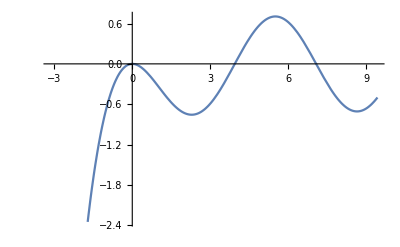

```mathematica
Plot[solDSolveValue,{x,-π,3π}]
```

Whereas the DSolve solution requires the use of a replacement rule to extract the function to plot:

```mathematica
Plot[Evaluate[y[x]/.solDSolve],{x,-π,3π}]
```

-Graphics-

If you want to plug the solution into some other equation, the DSolveValue solution requires a replacement rule, whereas the DSolve solution does not, as the rule is built into the solution:

```mathematica
otherEqn=(y[x]^2-y[x])^2;
```

```mathematica
otherEqn/.solDSolve[[1]]
otherEqn/.y[x]->solDSolveValue
```

(1/4 (-ⅇ^-x+Cos[x]-Sin[x])^2+1/2 (ⅇ^-x-Cos[x]+Sin[x]))^2

(1/4 (-ⅇ^-x+Cos[x]-Sin[x])^2+1/2 (ⅇ^-x-Cos[x]+Sin[x]))^2

However, if you are putting the solution into an equation that involves derivatives of the function, then both types of solutions will have problems because of the derivative terms:

```mathematica
eqn/.solDSolve[[1,1]]
```

1/2 (-ⅇ^-x+Cos[x]-Sin[x])+Sin[x]+y'[x]==0

```mathematica
eqn/.y[x]->solDSolveValue
```

1/2 (-ⅇ^-x+Cos[x]-Sin[x])+Sin[x]+y'[x]==0

```mathematica
(* eqn/.{solDSolve[[1,1]],D[solDSolve[[1,1]],x]} *)
```

```mathematica
(*eqn/.{y[x]->solDSolveValue,y'[x]-> D[solDSolveValue,x]}*)
```

### Dependent Variable: y

In the last calculation of the previous subsection, notice that y'[x] was not replaced. This is because the replacement rule just says how to replace y[x], not y'[x]. You need to include the derivative explicitly:

```mathematica
eqn/.{solDSolve[[1,1]],D[solDSolve[[1,1]],x]}
```

1/2 (ⅇ^-x-Cos[x]-Sin[x])+1/2 (-ⅇ^-x+Cos[x]-Sin[x])+Sin[x]==0

You can get the derivatives to be applied automatically by changing the second argument of DSolve or DSolveValue. This argument defines the dependent variable. Changing y[x] to y will change the form of the output:

```mathematica
solDSolveValue=DSolveValue[{eqn,cond},y,{x,-π,3π}]
solDSolve=DSolve[{eqn,cond},y,{x,-π,3π}]
```

Function[{x},1/2 (-ⅇ^-x+Cos[x]-Sin[x])]

{{y→Function[{x},1/2 (-ⅇ^-x+Cos[x]-Sin[x])]}}

Since the head of the function y is defined in the rule, rather than the y[x] function itself, the derivatives are automatically applied. This is very convenient when verifying the solution of a complicated equation:

```mathematica
eqn/.solDSolve[[1]]
```

1/2 (ⅇ^-x-Cos[x]-Sin[x])+1/2 (-ⅇ^-x+Cos[x]-Sin[x])+Sin[x]==0

You still need to define the replacement rule with the DSolveValue result:

```mathematica
eqn/. y->solDSolveValue
```

1/2 (ⅇ^-x-Cos[x]-Sin[x])+1/2 (-ⅇ^-x+Cos[x]-Sin[x])+Sin[x]==0

Plotting is done in the same way, only the argument x must be given to the functions explicitly:

```mathematica
Plot[solDSolveValue[x],{x,-π,3π}]
```

-Graphics-

```mathematica
Plot[y[x]/.solDSolve[[1]],{x,-π,3π}]
```

-Graphics-

### Equations with Multiple Solutions

NDSolveValue will only return one solution. If multiple solution branches exist, then NDSolveValue will only return the first solution and issue a warning message about the missing solutions:

```mathematica
NDSolveValue[{y'[x]^2-y[x]^2==0,y[0]^2==4},y[x],{x,1}]
```

NDSolveValue::ndsvb: There are multiple solution branches for the equations, but NDSolveValue will return only one. Use NDSolve to get all of the solution branches.

InterpolatingFunction[…][x]

```mathematica
NDSolve[{y'[x]^2-y[x]^2==0,y[0]^2==4},y[x],{x,1}]
```

{{y[x]→InterpolatingFunction[…][x]},{y[x]→InterpolatingFunction[…][x]},{y[x]→InterpolatingFunction[…][x]},{y[x]→InterpolatingFunction[…][x]}}

```mathematica
Clear["Global`*"]
```

## Specifying Derivative Boundary Conditions

There are several ways that derivative boundary conditions can be entered. Consider the following equation and condition:

```mathematica
eqn = f''[x]+f[x]==0;
cond=f[0]==1;
```

Suppose you would also like to specify the first derivative at x=0 as an additional condition. It may be tempting to use the following syntax, but this does not work:

```mathematica
D[f[0],x]
```

You need to take the derivative first with respect to a general x, then set x=0 afterward:

```mathematica
D[f[x],x]/.x->0
```

f'[0]

This should be used with caution, as multivariate functions do not accept the prime notation. The D function should be used in the multivariate case:

```mathematica
D[f[x,y],x]/.x->0
```

f^(1,0)[0,y]

Another alternative is to use the Derivative function. This allows you to take the derivative without needing to set x=0 afterward and works with multivariate functions:

```mathematica
Derivative[1][f][0]
Derivative[1,0][f][0,y]
```

f'[0]

f^(1,0)[0,y]

Finally, the partial derivative notation works as well:

```mathematica
D[ϕ[x,t], t,t]/.t->0
```

ϕ^(0,2)[x,0]

All four methods are valid for representing derivative boundary conditions in the single-variate case:

```mathematica
NDSolve[{eqn,cond,(D[f[x],x]/.x->0)==0},f,{x,0,10}];
NDSolve[{eqn,cond,f'[0]==0},f,{x,0,10}];
NDSolve[{eqn,cond,Derivative[1][f][0]==0},f,{x,0,10}];
NDSolve[{eqn,cond,(D[f[x], x]/.x->0)==0},f,{x,0,10}];
```

Notice that parentheses had to be used in (D[f[x],x]/.x→0)==0 to control the order of operations.

The syntax is analogous when working in the multivariate case:

```mathematica
L=4;
eqns={
D[u[t,x,y],{t,2}]==D[u[t,x,y],x,x]+D[u[t,x,y],y,y]+Sin[u[t,x,y]],
u[t,-L,y]==u[t,L,y],
u[t,x,-L]==u[t,x,L],
u[0,x,y]==Exp[-(x^2+y^2)]
};
```

```mathematica
NDSolve[{eqns,(D[u[t,x,y],t]/.t->0)==0},u,{t,0,L/2},{x,-L,L},{y,-L,L}];
NDSolve[{eqns,Derivative[1,0,0][u][0,x,y]==0},u,{t,0,L/2},{x,-L,L},{y,-L,L}];
sol=NDSolve[{eqns,(D[u[t,x,y], t]/.t->0)==0},u[t,x,y],{t,0,L/2},{x,-L,L},{y,-L,L}];
```

```mathematica
res=u[t,x,y]/.sol[[1]]
```

InterpolatingFunction[{{0., 2.}, {…, -4., 4., …}, {…, -4., 4., …}}, <>][t,x,y]

```mathematica
Plot3D[Evaluate[res/.t->1],{x,-4,4},{y,-4,4},ColorFunction->"CandyColors",PlotPoints->25,PlotRange->All]
```

-Graphics3D-

```mathematica
Clear["Global`*"]
```

## Automatic Adaptive Step Size

All numerical methods must discretize the independent variables with a certain step size. A larger step size results in a faster calculation but can decrease the accuracy of the result. Adaptive step-size methods try to balance and readjust these conflicting requirements along the integration path.

### Adaptive Step Sizes in NDSolve

NDSolve uses an adaptive procedure to determine the size of the steps in the independent variable. In general, if the solution varies rapidly in a particular region, NDSolve will reduce the step size to be able to better track the solution, then increase the step size when the solution varies more slowly.

Consider the following second-order ODE:

```mathematica
eqn=y''[x]+Sin[(1+50Exp[-10x^2])x]==0;
cond={y[0]==1,y'[0]==1/100};
sol=NDSolveValue[{eqn,cond},y[x],{x,-1,1}]
```

InterpolatingFunction[…][x]

Visualizing the solution:

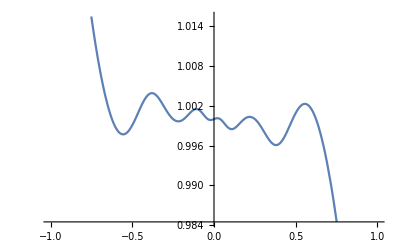

```mathematica
Plot[sol,{x,-1,1}]
```

The step sizes NDSolve used while solving the problem can be visualized with the DifferentialEquations`NDSolveUtilities` package, which gives access to the StepDataPlot function:

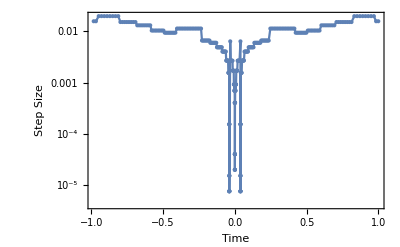

```mathematica
Needs["DifferentialEquations`NDSolveUtilities`"]
StepDataPlot[sol,FrameLabel-> {"Time",Rotate["Step Size",Pi/2]}]
```

```mathematica
Names["DifferentialEquations`NDSolveUtilities`*"]
```

{CompareMethods,FinalSolutions,InvariantDimensions,InvariantErrorFunction,InvariantErrorPlot,InvariantErrorSampleRate,RungeKuttaLinearStabilityFunction,StepDataCount,StepDataPlot}

```mathematica
Clear["Global`*"]
```

## NDSolve Options

NDSolve has many built-in options that allow the user to control the method that is used to solve a problem, the accuracy of the final result, the precision of the numbers used in the calculation and the maximum step size to use, and to monitor the calculation as it happens.

Options of particular importance are:

```mathematica
CellPrint@ExpressionCell[Grid[{
{Style["",Bold,20],SpanFromLeft},
{},
{Style["Option Name",Italic,16],Style["Default Value",Italic,16],Style["Description",Italic,16]},
{"Method","Automatic","Specifies the method to use with NDSolve."},
{"MaxSteps","Automatic", "Maximum number of steps to take."},
{"MaxStepSize","Automatic", "Maximum size of each step."},
{"StartingStepSize","Automatic","Specifies the initial step size to use in trying to generate results."},
{"AccuracyGoal","Automatic","Specifies the absolute tolerance to use in solving the nonlinear system."},
{"PrecisionGoal","Automatic","Specifies the relative tolerance to use in solving the nonlinear system."},
{"WorkingPrecision","MachinePrecision","Specifies how many digits of precision should be maintained in internal computations. "},
{"InterpolationOrder","Automatic","Specifies what order of interpolation to use."},
{"EvaluationMonitor","None","Gives an expression to evaluate whenever functions derived from the input are evaluated numerically. "},
{"StepMonitor","None","Gives an expression to evaluate whenever a step is taken by the numerical method used. "},
{"",SpanFromLeft}
},
Background->{None,{None,{LightBlue},None}},
Dividers->{{False},{False,{2->{RGBColor[0.85,0.5,0.4],Thick},4->GrayLevel[0.6]}}},
Spacings->{3,1},
ItemSize->{{10,10,40}},
Alignment->Left],"Output","GeneratedCell"->False]
```

|  | 
 |  | 
Option Name | Default Value | Description
Method | Automatic | Specifies the method to use with NDSolve.
MaxSteps | Automatic | Maximum number of steps to take.
MaxStepSize | Automatic | Maximum size of each step.
StartingStepSize | Automatic | Specifies the initial step size to use in trying to generate results.
AccuracyGoal | Automatic | Specifies the absolute tolerance to use in solving the nonlinear system.
PrecisionGoal | Automatic | Specifies the relative tolerance to use in solving the nonlinear system.
WorkingPrecision | MachinePrecision | Specifies how many digits of precision should be maintained in internal computations. 
InterpolationOrder | Automatic | Specifies what order of interpolation to use.
EvaluationMonitor | None | Gives an expression to evaluate whenever functions derived from the input are evaluated numerically. 
StepMonitor | None | Gives an expression to evaluate whenever a step is taken by the numerical method used. 
 |  |

### Example: Controlling Maximum Step Size

The step size can sometimes become quite large for some values of the independent variable. Large step sizes are one possible source of error in a solution.

Solve with the default options in NDSolve:

```mathematica
eqn=y''[x]+Sin[Log[x]]==0;
cond={y[1/100]==1,y'[1/100]==-1};
sol=NDSolve[{eqn,cond},y[x],{x,1/100,1}][[1]]
```

{y[x]→InterpolatingFunction[…][x]}

```mathematica
Needs["DifferentialEquations`NDSolveUtilities`"]//Quiet
```

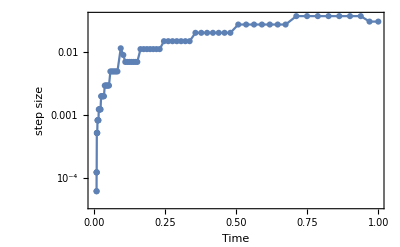

```mathematica
StepDataPlot[sol,FrameLabel->{"Time",Rotate["step size",Pi/2]}]
```

Specifying MaxStepSize will prevent the step size from getting too big. This comes with a computation cost, but may resolve some problems with numerical errors.

Solve the equation, but with a smaller maximum step size:

```mathematica
sol=NDSolve[{eqn,cond},y[x],{x,1/100,1},MaxStepSize->0.001];
```

Check the step sizes that were used. Notice the change in scale on the plot:

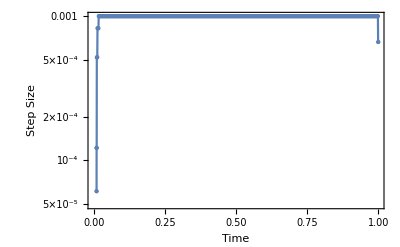

```mathematica
StepDataPlot[sol,FrameLabel->{"Time",Rotate["Step Size",Pi/2]}]
```

```mathematica
Clear["Global`*"]
```

## Summary

The Wolfram Language is a powerful tool for working with and solving differential equations. This section of the course covered:

Solving differential equations in the Wolfram Language

The basics of using NDSolve

Specifying boundary/initial conditions

Using the options to control the numerical accuracy of the solution

## Further Reading

#### Tutorials

Advanced Numerical Differential Equation Solving in the Wolfram Language

Numerical Solution of Differential Equations

#### Guides

Differential Equations

Partial Differential Equations

Differential Operators

### Glossary

```mathematica
{{"AsymptoticDSolveValue", "D", "Derivative", "DSolve", "DSolveValue"}, {"FullSimplify", "Grid", "Integrate", "MaxStepSize", "NDSolve"}, {"NDSolveValue", "Plot", "StepDataPlot", "TraditionalForm", ""}}
```